# The Use of CNN in Relating Precipitation to Circulation

## From Hourly to Monthly Scale

Baoxiang Pan
2017.7.13

## Introduction

Precipitation prediction in dynamical weather and climate models is built upon 1) the predictability of pressure or geopotential height for the forecasting period\cite[] and 2) the successive work of interpreting the pressure fields in terms of precipitation events\cite[].  Such strategy dates back to the early 20th century (Bjerknes)  and have ?? Empirical Extrapolating geopotential height field along time to numerical prediction. It helped the second task. (Existed works  connect to this target) tell about history of extrapolating during the very initial weather forecast semi-quantitative.

subsidiary work of interpreting the pressure field in terms of weather also demands  a large share of attention and is somewhat complex.

Correlation field.

the second task: 
1) focusing on prediction
  	1.1) parameterization
		microphysics
		cumulative parameter 
  	1.2) cloud resolving models
2) focusing on interpretation
	2.1) Correlation Field
	2.2) PCA Combined PCA
What have been done in interpreting?
what are their drawbacks?
This study is directed toward one aspect of the subsidiary problem. 
What have been done in interpreting?
Deep learning quantitative observation.	
1) understanding
2) diagnosis: Typical pressure structure, intensity, distance, evolution 
3) improvement

## Data

Precipitation (all measured in mm/hr)

#### NCEP_Reanalysis

```mathematica
NCEPprecip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]];
	mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]];	
	Table[Import["prate.sfc.gauss."<>ToString[year]<>".nc",{"Datasets","prate"}][[;;,21;;31,126;;133]]*3600,
		{year,1948,2006}]];
Block[{mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]],
	   mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]]},
	{MinMax[mlat],MinMax[mlon]}]
```

#### ECMWF_Reanalysis

#### CPC_Gauge

```mathematica
SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
year=1948;
precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
mlat=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lat"}][[48;;]];
mlon=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lon"}][[21;;65]];
precip=precip /. x_/; x< 0 ->nan;
precip[[;;,32;;,26;;]]=nan;
Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	   t,tt},s
	t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
	tt=Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t];
	Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt]];
```

```mathematica
precip=Block[{mlat,mlon,tt},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	mlat=Import["precip.V1.0.1948.nc",{"Datasets","lat"}][[48;;]];
	mlon=Import["precip.V1.0.1948.nc",{"Datasets","lon"}][[21;;65]];
	tt=Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],
	       t},
			t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
			Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t]];
	Table[Block[{precip},
		precip=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
		precip=precip /. x_/; x< 0 ->nan;
		precip[[;;,32;;,26;;]]=nan;
		Map[Set[precip[[;;,#[[1]],#[[2]]]],nan]&,tt];
		precip],{year,1948,2006}]];
```

Sea Level Pressure

#### NCEP_Reanalysis

```mathematica
SLP=Block[{mlat,mlon,slat=10,elat=30,slon=85,elon=105},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/SLP"];
	mlat=Import["slp.1948.nc",{"Datasets","lat"}][[slat;;elat]];
	mlon=Import["slp.1948.nc",{"Datasets","lon"}][[slon;;elon]];
	Table[Import["slp."<>ToString[year]<>".nc",{"Datasets","slp"}][[;;,slat;;elat,slon;;elon]],
		{year,1948,2006}]];
```

```mathematica
Dimensions[precip[[1]]]
Dimensions[SLP[[1]]]
```

{1464,11,8}

{1464,21,21}

#### ECMWF_Reanalysis

## Methodology

```mathematica
winter=Flatten[Table[{Range[1+year*365*4,90*4+year*365*4],Range[270*4+year*365*4,365.25*4+year*365*4]},{year,0,58}]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43694,86100,86101,86102,86103,86104,86105,86106,86107,86108,86109,86110,86111,86112,86113,86114,86115,86116,86117,86118,86119,86120,86121,86122,86123,86124,86125,86126,86127,86128,86129,86130,86131,86132,86133,86134,86135,86136,86137,86138,86139,86140,86141}
 |  |  |  |

```mathematica
Precip=Block[{m=Mean[Flatten[precip,1]]},
	Map[15000*Flatten[#-m]&,Flatten[precip,1]]][[winter]];
Slp=Block[{m=Mean[Flatten[SLP,1]]},
	Map[{#-m}/900.&,Flatten[SLP,1]]][[winter]];
Dimensions[Precip]
Dimensions[Slp]
{Precip,Slp}=Block[{tempt=RandomSample[Table[{Precip[[i]],Slp[[i]]},{i,Length[Slp]}]]},
	{Map[#[[1]]&,tempt],Map[#[[2]]&,tempt]}];
Dimensions[Precip]
Dimensions[Slp]
```

{43778,88}

{43778,1,21,21}

{43778,88}

{43778,1,21,21}

```mathematica
tempt=Precip[[;;,15]];
```

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 300,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 200,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.2],
						 
						 BatchNormalizationLayer[],
						 1(*,
						 BatchNormalizationLayer[]*)
						 (*ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[]*)
						 },  
					"Input" -> {1,21,21},
					"Output" -> "Scalar"]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[Slp]*0.7]
```

30644

```mathematica
Dimensions[tempt]
```

{43778}

```mathematica
ann=NetTrain[CNN,
	Slp[[1;;ptraining]]->tempt[[1;;ptraining]],
	ValidationSet->Table[Slp[[i]]->tempt[[i]],{i,ptraining,Length[Slp]}],
	Method->"ADAM",
	BatchSize->500,
	MaxTrainingRounds -> 2000]
```

NetChain[]

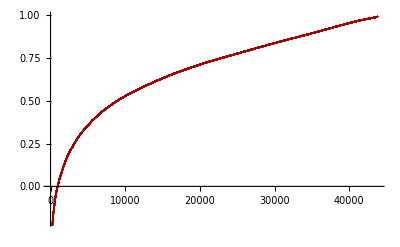

0.67786

```mathematica
test=Table[Correlation[Precip[[day]], ann@Slp[[day]]],{day,Length[Slp]}];
ListPlot[Sort[test]]
Mean[test]
```

31750

ListPlot::lpn: -0.193501 is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{-0.721442,-0.667602,-0.566449,-0.405408,-0.270455,-0.203618,-0.19876,-0.241847,-0.757909,«33»,-0.418481,-0.2278,-0.147803,-0.170987,-0.189625,-0.191452,-0.224454,-0.303386,«38»},-«20»} cannot be transposed.

ListPlot::lpn: Transpose[{{-0.721442,-0.667602,-0.566449,-0.405408,-0.270455,-0.203618,-0.19876,-0.241847,-0.757909,«33»,-0.418481,-0.2278,-0.147803,-0.170987,-0.189625,-0.191452,-0.224454,-0.303386,«38»},«1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

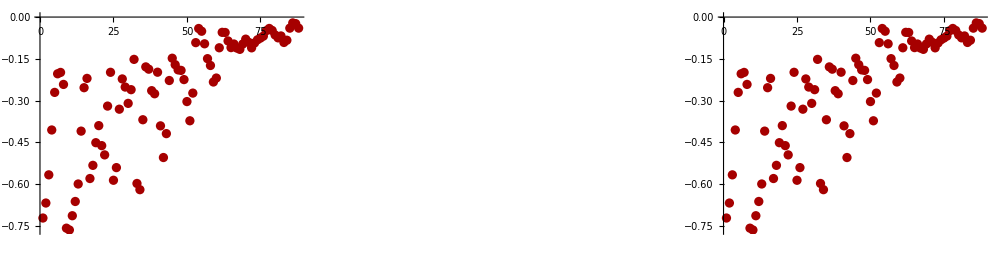

```mathematica
day=Position[test,Max[test]][[1,1]]
GraphicsRow[{ListPlot[Precip[[day]],PlotRange->Full],
			 ListPlot[ann@Slp[[day]],PlotRange->Full],
			 ListPlot[{Precip[[day]], ann@Slp[[day]]},PlotRange->Full],
			 ListPlot[Transpose[{Precip[[day]], ann@Slp[[day]]}],PlotRange->Full]},ImageSize->1000]
```

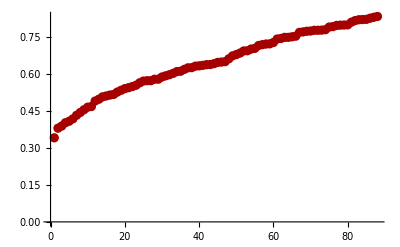

```mathematica
simu=Table[ann@Slp[[day]],{day,Length[Slp]}];
te=Table[Correlation[simu[[;;,i]],Precip[[;;,i]]],{i,88}];
ListPlot[Sort[te]]
```

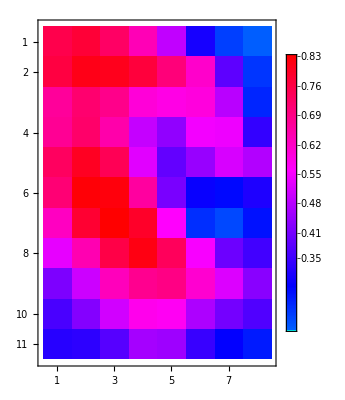

```mathematica
MatrixPlot[ArrayReshape[te,{11,8}],ColorFunction->Hue,
	PlotLegends->Automatic]
```

```mathematica
Dimensions[precip[[1]]]
```

{1464,11,8}

```mathematica
SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	mlat=Import["prate.sfc.gauss.1948.nc",{"Datasets","lat"}][[21;;31]]
	mlon=Import["prate.sfc.gauss.1948.nc",{"Datasets","lon"}][[126;;133]]
```

{50.4752,48.5705,46.6658,44.7611,42.8564,40.9517,39.047,37.1422,35.2375,33.3328,31.4281}

{234.375,236.25,238.125,240.,241.875,243.75,245.625,247.5}

## Results

## Discussion

## Conclusion

```mathematica
SetDirectory["/Users/lambda/Documents/S2S/Results"];
Export["ANN.txt",ann]
```

ANN.txt

## Network Structure

```mathematica
Precip=Block[{tempt=Map[Select[Flatten[#],NumberQ]&,Flatten[precip,1]],m,v},
	 v=Sqrt[Variance[tempt]];
	 m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[Precip]
```

{21550,1450}

```mathematica
SLP=Block[{tempt=Flatten[slp,1],m,v},
	v=Sqrt[Variance[tempt]];
	m=Mean[tempt];
	Map[(#-m)/v&,tempt]];
Dimensions[SLP]
```

{21550,16,11}

```mathematica
winter=Flatten[Table[{Range[1+year*365,90+year*365],Range[275+year*365,365+year*365]},{year,0,58}]];
```

```mathematica
Precip=Precip[[winter]];
SLP=SLP[[winter]];
```

```mathematica
CNN=NetInitialize[NetChain[{ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2,1],
						 ConvolutionLayer[1, 3], 
						 ElementwiseLayer[Ramp],
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.5],
						 BatchNormalizationLayer[],
						 900,
						 ElementwiseLayer[Ramp],
						 900,
						 ElementwiseLayer[Ramp],
						 1450,
						 BatchNormalizationLayer[]},  
					"Input" -> {1,16,11}]]
```

NetChain[]

```mathematica
ptraining=Floor[Length[SLP]*0.7]
```

7475

```mathematica
ann = NetTrain[CNN,
	Map[{#}&,SLP[[1;;ptraining]]] -> Precip[[1;;ptraining]],
	ValidationSet->Table[{SLP[[i]]}->Precip[[i]],{i,ptraining,Length[SLP]}],
	Method->"ADAM",
	BatchSize->200,
	MaxTrainingRounds -> 2000]
```

NetChain[]

```mathematica
Dimensions[SLP]
```

{10679,16,11}

```mathematica
simu=Table[ann@{SLP[[day]]},{day,Length[SLP]}];
```

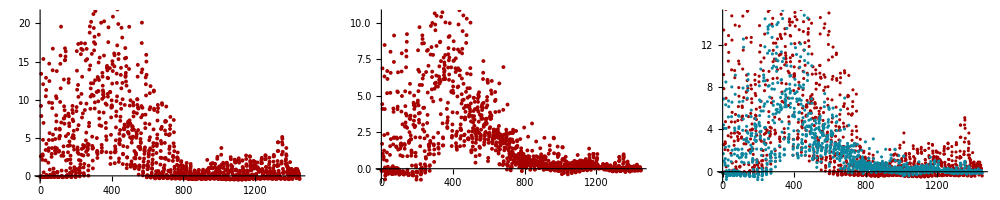

```mathematica
day=3419;
GraphicsRow[{ListPlot[Precip[[day]]],ListPlot[ann@{SLP[[day]]}],ListPlot[{Precip[[day]],ann@{SLP[[day]]}}]},
	ImageSize->1000]
```

```mathematica
test=Table[Correlation[ann@{SLP[[day]]},Precip[[day]]],{day,Length[SLP]}];
```

```mathematica
MinMax[test]
```

{-0.656667,0.973372}

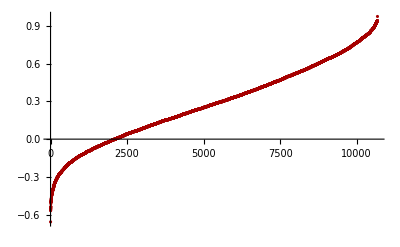

```mathematica
ListPlot[Sort[test]]
```

```mathematica
Position[test,Max[test[[1;;365*10]]]]
```

{{3419}}

### Second level section heading

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.